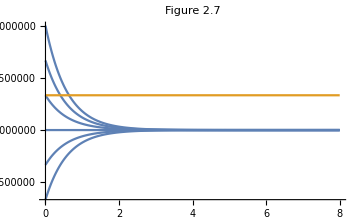

```mathematica
Module[{cin,V,F,c0},
cin=3 10^6;
V=28 10^6;
F=4 10^6*12;
c0 = {1,2,3,4,5,6}10^6;
Plot[{cin-(cin-c0[[#]])ⅇ^(-F/V t),4 10^6},{t,0,8},PlotRange->All,PlotLabel->"Figure 2.7",ImageSize->Medium]&[{1,2,3,4,5,6}]]
```

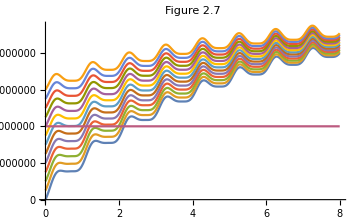

```mathematica
Module[{cin,V,F,c0,conc},
cin[t_]=10^6(10+10Cos[2π t]);
V=28 10^6;
F[t_]=10^6 (6+6Sin[2π t]);
c0 = Table[n,{n,0,6,.5}] 10^6;
conc=C[t]/.NDSolve[{C'[t]==F[t]/V cin[t]-F[t]/V C[t],C[0]==#},C[t],{t,0,8}]&/@c0;
Plot[{conc,4 10^6},{t,0,8},PlotRange->All,PlotLabel->"Figure 2.7",ImageSize->Medium]]
```